Rechnung zu zwei Solitonen

Rechnung für konstante und kosinusförmige effektive Geschwindigkeit

2 Solitonen, v = const. , ϵ = ϵ0 cos(π/2m ϕ)

```mathematica
(*Parameter definieren*)
Ntrunc=100;    (*Trunkierung:n von-Ntrunc bis Ntrunc*)
m=1;

buildHMatrixVconst[Nmax_,m_,v_,em_]:=Module[{dim,M,pos,n,posAn,posBn,posAnm,posBnm,posAnp,posBnp},dim=2*(2*Nmax+1);(*Dimension des Vektors*)M=ConstantArray[0,{dim,dim}];
(*Hilfsfunktion zur Indexberechnung*)pos[n_]:=2*(Nmax-n);
(*Position von a_n*)Do[posAn=pos[n]+1;(*1-basierte Position für a_n*)posBn=pos[n]+2;(*1-basierte Position für b_n*)
(*Erste Gleichung:v*n*b_n+(em/2)(a_{n-m}+a_{n+m})=E*a_n*)
M[[posAn,posBn]]=v/2(n+1/2);(*b_n-Term*)
(*a_{n-m} Term*)If[Abs[n-m]<=Nmax,posAnm=pos[n-m]+1;
M[[posAn,posAnm]]+=em/2;];
(*a_{n+m} Term*)If[Abs[n+m]<=Nmax,posAnp=pos[n+m]+1;
M[[posAn,posAnp]]+=em/2;];

(*Zweite Gleichung:v*n*a_n-(em/2)(b_{n-m}+b_{n+m})=E*b_n*)
M[[posBn,posAn]]=v/2(n+1/2);(*a_n-Term*)
(*b_{n-m} Term*)If[Abs[n-m]<=Nmax,posBnm=pos[n-m]+2;
M[[posBn,posBnm]]-=em/2;];
(*b_{n+m} Term*)If[Abs[n+m]<=Nmax,posBnp=pos[n+m]+2;
M[[posBn,posBnp]]-=em/2;],{n,-Nmax,Nmax}];
M];
M=buildHMatrixVconst[Ntrunc,m,v,ϵ0];

Print["Matrix M erstellt. Dimension: ",2*(2*Ntrunc+1),"x",2*(2*Ntrunc+1)];
MatrixForm[M];
```

Matrix M erstellt. Dimension: 402x402

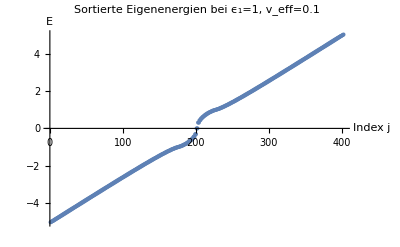

```mathematica
ϵ0Value=1;
vValue=0.1;

Plots={};
valsUvecs={};


{vals,vecs}=Eigensystem[M/. {ϵ0->ϵ0Value,v->vValue}];
AppendTo[valsUvecs,{vals,vecs}];
Print[ListPlot[{Sort[vals]},PlotLabel->"Sortierte Eigenenergien bei ϵ_1="<>ToString[ϵ0Value]<>", v_eff="<> ToString[vValue],AxesLabel->{"Index j","E"}]];
```

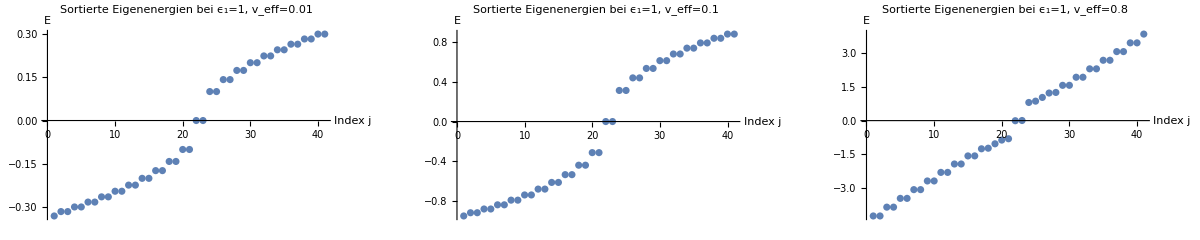

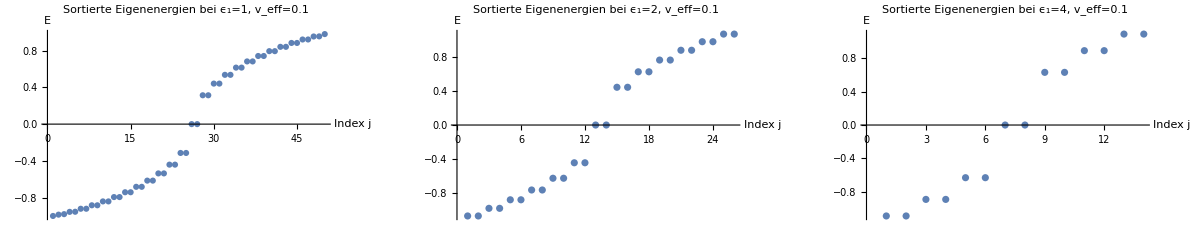

```mathematica
ϵ0Values={1,1,1};
vValues={0.01,0.1,0.8};

Plots={};
valsUvecs={};

For[i=1,i<=Length[ϵ0Values],i++,
{vals,vecs}=Eigensystem[M/. {ϵ0->ϵ0Values[[i]],v->vValues[[i]]}];AppendTo[valsUvecs,{vals,vecs}];plot=ListPlot[{Sort[vals][[180;;220]]},PlotLabel->"Sortierte Eigenenergien bei ϵ_1="<>ToString[ϵ0Values[[i]]]<>", v_eff="<> ToString[vValues[[i]]],AxesLabel->{"Index j","E"}];
AppendTo[Plots,plot]
]
GraphicsRow[Plots,ImageSize->Full]



ϵ0Values={1,2,4};
vValues={0.1,0.1,0.1};
lowerCuttingArea={176,189,195};
upperCuttingArea={225,214,208};

Plots={};
valsUvecs={};

For[i=1,i<=Length[ϵ0Values],i++,
{vals,vecs}=Eigensystem[M/. {ϵ0->ϵ0Values[[i]],v->vValues[[i]]}];AppendTo[valsUvecs,{vals,vecs}];plot=ListPlot[{Sort[vals][[lowerCuttingArea[[i]];;upperCuttingArea[[i]]]]},PlotLabel->"Sortierte Eigenenergien bei ϵ_1="<>ToString[ϵ0Values[[i]]]<>", v_eff="<> ToString[vValues[[i]]],AxesLabel->{"Index j","E"}];
AppendTo[Plots,plot]
]
GraphicsRow[Plots,ImageSize->Full]
```

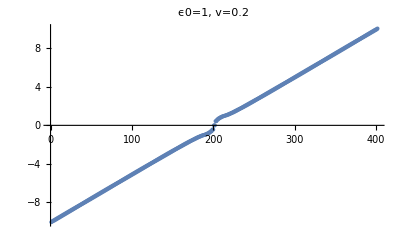

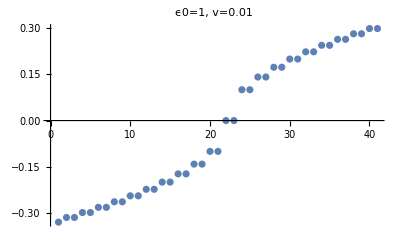

```mathematica
ϵTestSingle=1;
vTestSingle=0.2;
{NeigvalsSingle1,NeigvecsSingle1}=Eigensystem[M/.{ϵ0->ϵTestSingle,v->vTestSingle}];
ListPlot[Sort[Re[NeigvalsSingle1]],
PlotLabel->"ϵ0="<>ToString[ϵTestSingle]<>", v="<> ToString[vTestSingle]]


ϵTestSingle=1;
vTestSingle=0.01;
{NeigvalsSingle1,NeigvecsSingle1}=Eigensystem[M/.{ϵ0->ϵTestSingle,v->vTestSingle}];
ListPlot[Sort[Re[NeigvalsSingle1]][[180;;220]],
PlotLabel->"ϵ0="<>ToString[ϵTestSingle]<>", v="<> ToString[vTestSingle]]
```

```mathematica
ϵTestSingle=1;
vTestSingle=0.1;
{NeigvalsSingle1,NeigvecsSingle1}=Eigensystem[M/.{ϵ0->ϵTestSingle,v->vTestSingle}];
{sortedNeigvalsSingle,sortedNeigvecsSingle}=Transpose[SortBy[Transpose[{NeigvalsSingle1,NeigvecsSingle1}],First]];
```

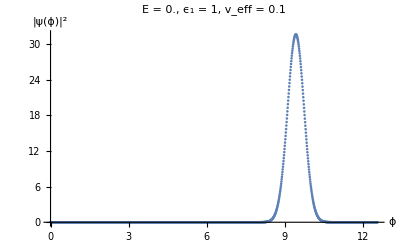

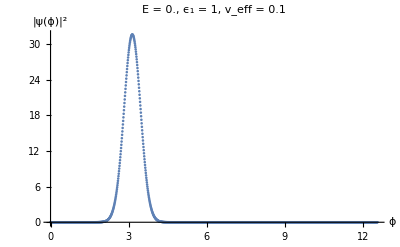

```mathematica
positions={201};

For[i=1,i<=Length[positions],i++,
pos=positions[[i]];
nValues=Range[-Ntrunc,Ntrunc];
vector1=E^(I*nValues/2 ϕ);
ψ1=Total[sortedNeigvecsSingle[[pos]][[1;;-1;;2]]*vector1];
ψ2=Total[sortedNeigvecsSingle[[pos]][[2;;-1;;2]]*vector1];
ψ3=Total[sortedNeigvecsSingle[[pos+1]][[1;;-1;;2]]*vector1];
ψ4=Total[sortedNeigvecsSingle[[pos+1]][[2;;-1;;2]]*vector1];
phase1={E^(I*Pi/2) ,1};
phase2={1,E^(I*Pi/2)};
For[j=1,j<=Length[phase1],j++,
ψp={ψ1*phase1[[j]]+ψ3*phase2[[j]],ψ2*phase1[[j]]+ψ4*phase2[[j]]};
ψ=Conjugate[ψp].ψp;
Print[ListPlot[
Table[{ϕ,Re[ψ]},{ϕ,0,4 Pi,0.01}],
PlotRange->All,AxesLabel->{"ϕ","|ψ(ϕ)|^2"},PlotLabel->"E = "<>ToString[Round[sortedNeigvalsSingle[[pos]],0.001]]<>", ϵ_1 = "<>ToString[ϵTestSingle]<>", v_eff = "<>ToString[vTestSingle]]]
]]
```

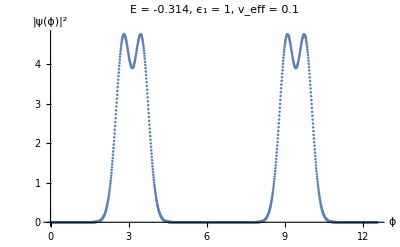

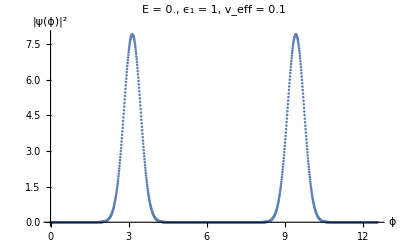

-Graphics-

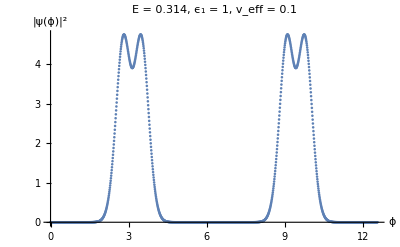

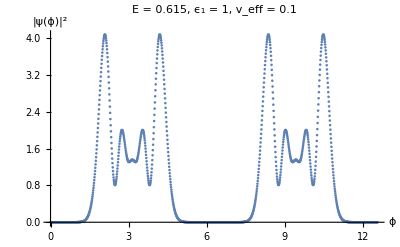

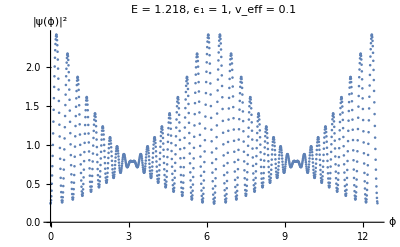

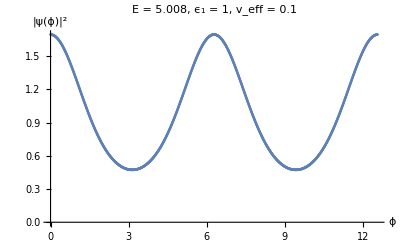

```mathematica
positions={200,201,202,203,210,240,400};

For[i=1,i<=Length[positions],i++,
pos=positions[[i]];
nValues=Range[-Ntrunc,Ntrunc];
vector1=E^(I*nValues/2 ϕ);
ψ1=Total[sortedNeigvecsSingle[[pos]][[2;; ;;2]]*vector1];
ψ2=Total[sortedNeigvecsSingle[[pos]][[1;; ;;2]]*vector1];
ψ=Conjugate[{ψ1,ψ2}].{ψ1,ψ2};
Print[ListPlot[
Table[{ϕ,Re[ψ]},{ϕ,0,4 Pi,0.01}],
PlotRange->All,AxesLabel->{"ϕ","|ψ(ϕ)|^2"},PlotLabel->"E = "<>ToString[Round[sortedNeigvalsSingle[[pos]],0.001]]<>", ϵ_1 = "<>ToString[ϵTestSingle]<>", v_eff = "<>ToString[vTestSingle]]]
]
```

2 Solitonen, v = v0 + v1 cos(π/2mv)  , ϵ = .08ϵ0 cos(π/2m ϕ)

```mathematica
(*Parameter definieren*)
Ntrunc=100;    (*Trunkierung:n von-Ntrunc bis Ntrunc*)
m=2;
l=1;

buildHMatrix[Nmax_,m_,l_,v0_,v1_,e_]:=Module[{dim,M,pos,n,posAn,posBn,posAnm,posBnm,posAnp,posBnp,posAnlm,posAnlp,posBnlm,posBnlp},dim=2*(2*Nmax+1);(*Dimension des Vektors*)M=ConstantArray[0,{dim,dim}];
(*Hilfsfunktion zur Indexberechnung*)pos[n_]:=2*(Nmax-n);
Do[(*Positionen für a_n und b_n*)posAn=pos[n]+1;(*1-basierte Position für a_n*)posBn=pos[n]+2;(*1-basierte Position für b_n*)
(*Erste Gleichung:v0*n*a_n+v1*(n*m*b_{n-m}+n*m*b_{n+m})+e*(a_{n-l}+a_{n+l})=E*a_n*)
(*Diagonalelement für a_n*)M[[posAn,posAn]]=1/2 v0*(n+1/2);
(*b_{n-m} Term*)If[Abs[n-m]<=Nmax,posBnm=pos[n-m]+2;
M[[posAn,posBnm]]+=1/4 v1*(n-m+m/2+1/2);];
(*b_{n+m} Term*)If[Abs[n+m]<=Nmax,posBnp=pos[n+m]+2;
M[[posAn,posBnp]]+=1/4 v1*(n+m-m/2+1/2);];
(*a_{n-l} Term*)If[Abs[n-l]<=Nmax,posAnlm=pos[n-l]+1;
M[[posAn,posAnlm]]+=1/2 e;];
(*a_{n+l} Term*)If[Abs[n+l]<=Nmax,posAnlp=pos[n+l]+1;
M[[posAn,posAnlp]]+=1/2 e;];


(*Zweite Gleichung:v0*n*b_n+v1*(n*m*a_{n-m}+n*m*a_{n+m})-e*(b_{n-l}+b_{n+l})=E*b_n*)
(*Diagonalelement für b_n*)M[[posBn,posBn]]=1/2 v0*(n+1/2);
(*a_{n-m} Term*)If[Abs[n-m]<=Nmax,posAnm=pos[n-m]+1;
M[[posBn,posAnm]]+=1/4 v1*(n-m+m/2+1/2);];
(*a_{n+m} Term*)If[Abs[n+m]<=Nmax,posAnp=pos[n+m]+1;
M[[posBn,posAnp]]+=1/4 v1*(n+m-m/2+1/2);];
(*b_{n-l} Term*)If[Abs[n-l]<=Nmax,posBnlm=pos[n-l]+2;
M[[posBn,posBnlm]]-=1/2 e;];
(*b_{n+l} Term*)If[Abs[n+l]<=Nmax,posBnlp=pos[n+l]+2;
M[[posBn,posBnlp]]-=1/2 e;];,{n,-Nmax,Nmax}];
M];

(*Matrix erstellen*)
Mv=buildHMatrix[Ntrunc,m,l,v0,v1,ϵ0];

Print["Matrix Mv erstellt. Dimension: ",2*(2*Ntrunc+1),"x",2*(2*Ntrunc+1)];
MatrixForm[Mv];
```

Matrix Mv erstellt. Dimension: 402x402

```mathematica
ϵ0Values={1,1,1,1,1,1,1};
v0Values={0.9,0.5,0.1,0.01,0.001,0.0001,0.00001};
v1Values={0.3,0.2,0.05,0.01,0.001,0.0001,0.00001};

valsUvecs={};

(*
For[i=1,i<=Length[ϵ0Values],i++,{vals,vecs}=Eigensystem[Mv/. {ϵ0->ϵ0Values[[i]],v0->v0Values[[i]],v1->v1Values[[i]]}];AppendTo[valsUvecs,{vals,vecs}];Print[ListPlot[{Labeled[Sort[Re[vals]],"Re"],Labeled[Sort[Im[vals]],"Im"]},PlotLabel->"ϵ0="<>ToString[ϵ0Values[[i]]]<>", v0="<> ToString[v0Values[[i]]]<>", v1="<> ToString[v1Values[[i]]]]]]*)

ϵ0Value=1;
PlotTablev={};
For[i=1,i<=Length[ϵ0Values],i++,
sysPart={};
plotPart={};
For[j=1,j<=Length[v0Values],j++,
{vals,vecs}=Eigensystem[Mv/. {ϵ0->ϵ0Value,v0->v0Values[[i]],v1->v1Values[[j]]}];
AppendTo[sysPart,{vals,vecs}];
plot=ListPlot[Sort[vals][[180;;220]],PlotLabel->"ϵ0="<>ToString[ϵ0Value]<>", v0="<> ToString[v0Values[[i]]]<>", v1="<> ToString[v1Values[[j]]]];
Print["Plot "<>i<>j<>" completed."];
AppendTo[plotPart,plot];
];
AppendTo[valsUvecs,sysPart];
AppendTo[PlotTablev,plotPart];
]
```

StringJoin::string: String expected at position 2 in Plot <>1<>1<> completed..

StringJoin::string: String expected at position 3 in Plot <>1<>1<> completed..

Plot <>1<>1<> completed.

StringJoin::string: String expected at position 2 in Plot <>1<>2<> completed..

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Plot <>1<>2<> completed.

Plot <>1<>3<> completed.

Plot <>1<>4<> completed.

Plot <>1<>5<> completed.

Plot <>1<>6<> completed.

Plot <>1<>7<> completed.

Plot <>2<>1<> completed.

Plot <>2<>2<> completed.

Plot <>2<>3<> completed.

Plot <>2<>4<> completed.

Plot <>2<>5<> completed.

Plot <>2<>6<> completed.

Plot <>2<>7<> completed.

Plot <>3<>1<> completed.

Plot <>3<>2<> completed.

Plot <>3<>3<> completed.

Plot <>3<>4<> completed.

Plot <>3<>5<> completed.

Plot <>3<>6<> completed.

Plot <>3<>7<> completed.

Plot <>4<>1<> completed.

Plot <>4<>2<> completed.

Plot <>4<>3<> completed.

Plot <>4<>4<> completed.

Plot <>4<>5<> completed.

Plot <>4<>6<> completed.

Plot <>4<>7<> completed.

Plot <>5<>1<> completed.

Plot <>5<>2<> completed.

Plot <>5<>3<> completed.

Plot <>5<>4<> completed.

Plot <>5<>5<> completed.

Plot <>5<>6<> completed.

Plot <>5<>7<> completed.

Plot <>6<>1<> completed.

Plot <>6<>2<> completed.

Plot <>6<>3<> completed.

Plot <>6<>4<> completed.

Plot <>6<>5<> completed.

Plot <>6<>6<> completed.

Plot <>6<>7<> completed.

Plot <>7<>1<> completed.

Plot <>7<>2<> completed.

Plot <>7<>3<> completed.

Plot <>7<>4<> completed.

Plot <>7<>5<> completed.

Plot <>7<>6<> completed.

Plot <>7<>7<> completed.

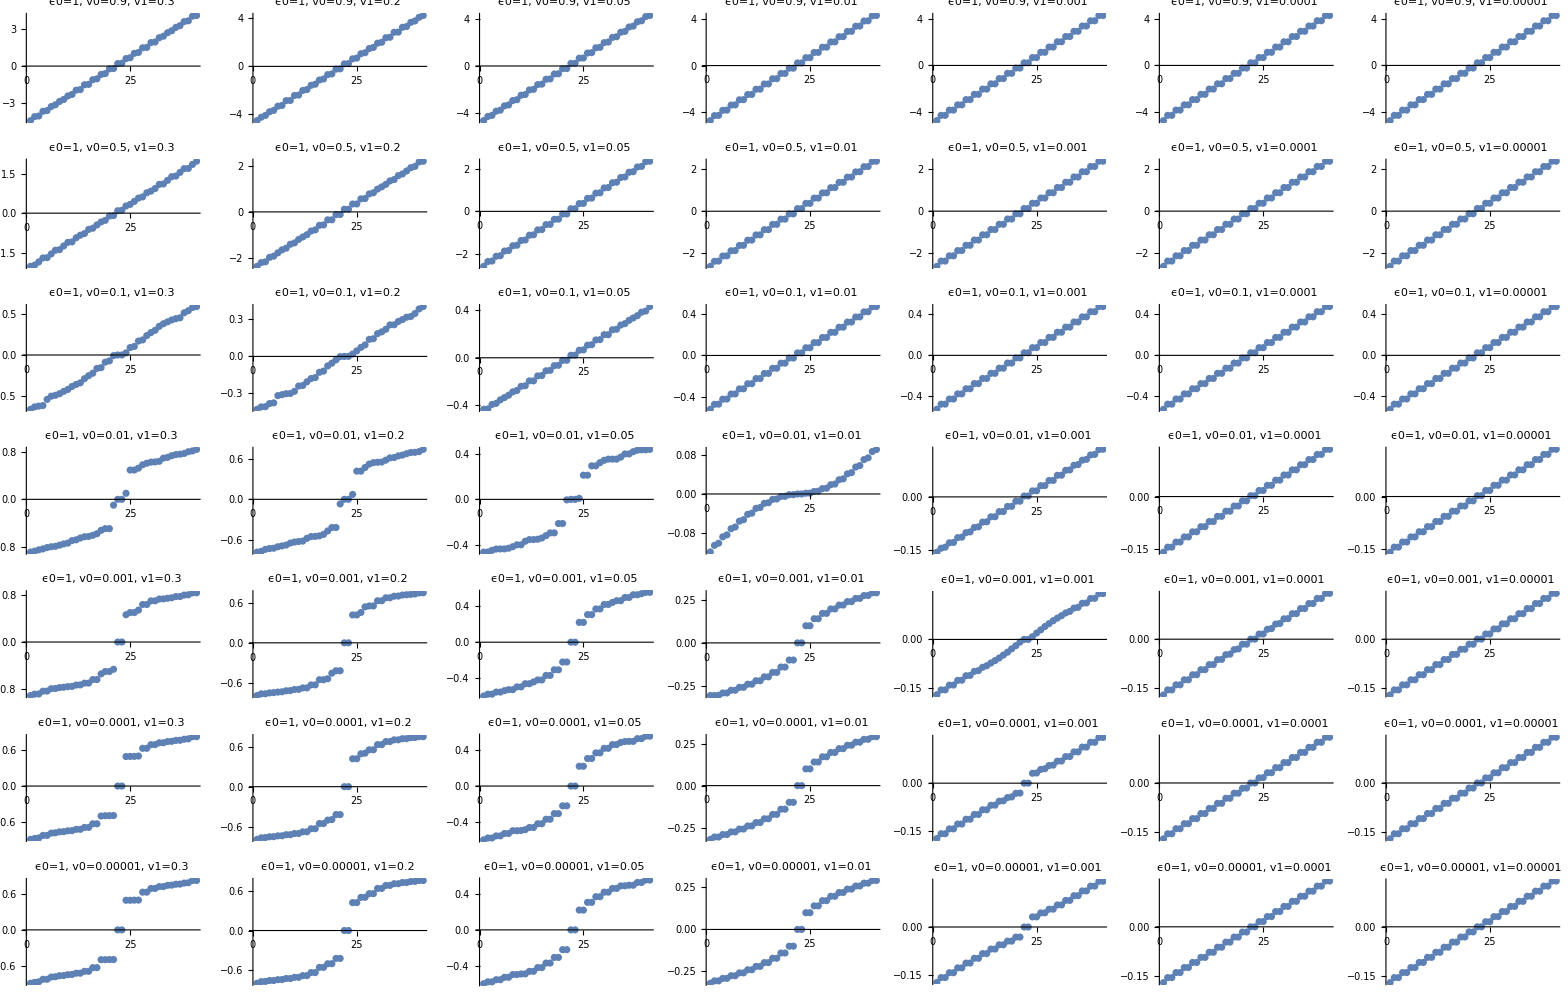

```mathematica
GraphicsGrid[PlotTablev,ImageSize->Full]
```

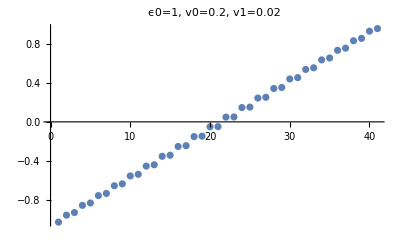

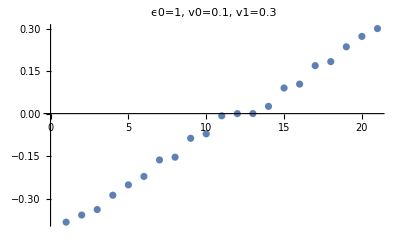

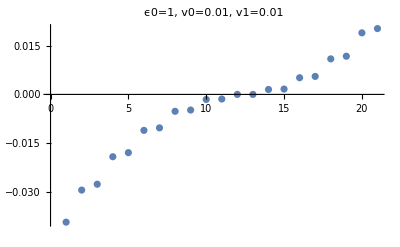

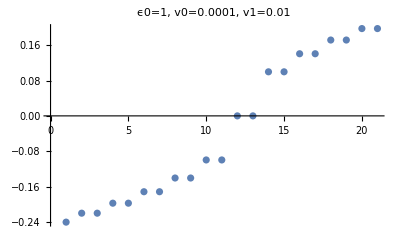

```mathematica
ϵ0TestSingle=1;
v0TestSingle=0.2;
v1TestSingle=0.02;
{NeigvalsSingle1,NeigvecsSingle1}=Eigensystem[Mv/.{ϵ0->ϵ0TestSingle,v0->v0TestSingle,v1->v1TestSingle}];
ListPlot[Sort[NeigvalsSingle1][[180;;220]],
PlotLabel->"ϵ0="<>ToString[ϵ0TestSingle]<>", v0="<> ToString[v0TestSingle]<>", v1="<> ToString[v1TestSingle]]


ϵ0TestSingle=1;
v0TestSingle=0.1;
v1TestSingle=0.3;
{NeigvalsSingle2,NeigvecsSingle2}=Eigensystem[Mv/.{ϵ0->ϵ0TestSingle,v0->v0TestSingle,v1->v1TestSingle}];
ListPlot[Sort[NeigvalsSingle2][[190;;210]],
PlotLabel->"ϵ0="<>ToString[ϵ0TestSingle]<>", v0="<> ToString[v0TestSingle]<>", v1="<> ToString[v1TestSingle]]


ϵ0TestSingle=1;
v0TestSingle=0.01;
v1TestSingle=0.01;
{NeigvalsSingle3,NeigvecsSingle3}=Eigensystem[Mv/.{ϵ0->ϵ0TestSingle,v0->v0TestSingle,v1->v1TestSingle}];
ListPlot[Sort[NeigvalsSingle3][[190;;210]],
PlotLabel->"ϵ0="<>ToString[ϵ0TestSingle]<>", v0="<> ToString[v0TestSingle]<>", v1="<> ToString[v1TestSingle]]


ϵ0TestSingle=1;
v0TestSingle=0.0001;
v1TestSingle=0.01;
{NeigvalsSingle4,NeigvecsSingle4}=Eigensystem[Mv/.{ϵ0->ϵ0TestSingle,v0->v0TestSingle,v1->v1TestSingle}];
ListPlot[Sort[NeigvalsSingle4][[190;;210]],
PlotLabel->"ϵ0="<>ToString[ϵ0TestSingle]<>", v0="<> ToString[v0TestSingle]<>", v1="<> ToString[v1TestSingle]]
```

```mathematica
{sortedNeigvalsSingle,sortedNeigvecsSingle}=Transpose[SortBy[Transpose[{NeigvalsSingle4,NeigvecsSingle4}],First]];
```

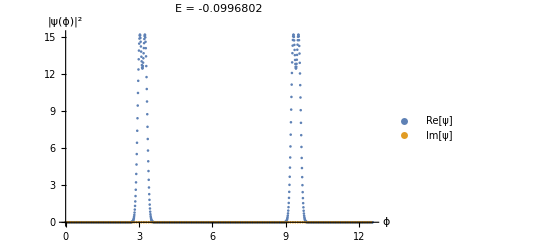

-Graphics-

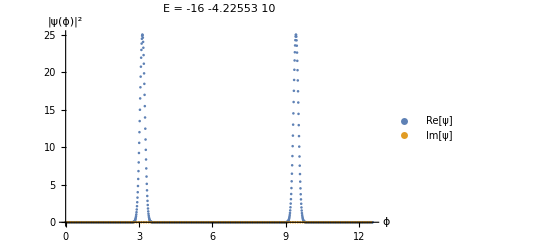

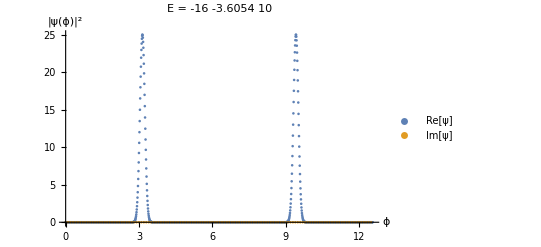

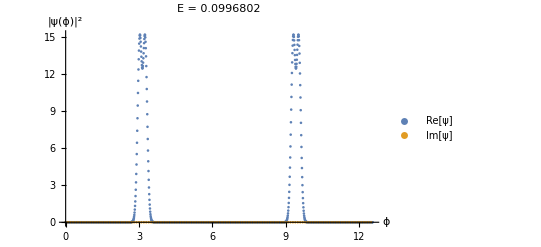

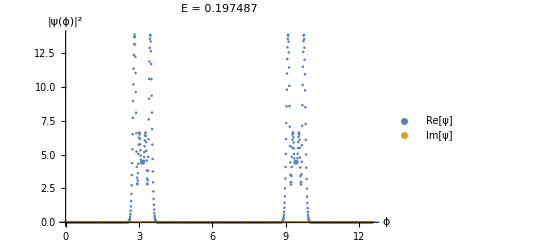

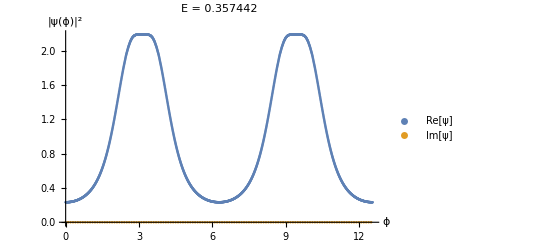

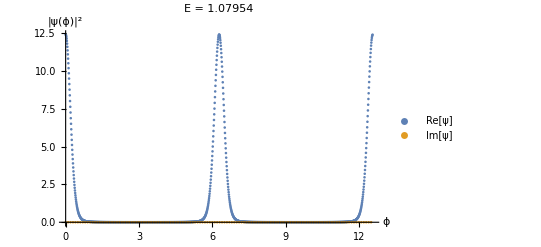

```mathematica
positionsv={199,200,201,202,203,210,230,400};

For[i=1,i<=Length[positionsv],i++,
pos=positionsv[[i]];
nValues=Range[-Ntrunc,Ntrunc];
vector1v=E^(I*nValues/2 ϕ);
ψ1v=Total[sortedNeigvecsSingle[[pos]][[2;; ;;2]]*vector1v];
ψ2v=Total[sortedNeigvecsSingle[[pos]][[1;; ;;2]]*vector1v];
ψv=Conjugate[{ψ1v,ψ2v}].{ψ1v,ψ2v};
Print[ListPlot[{
Table[{ϕ,Re[ψv]},{ϕ,0,4 Pi,0.01}],
Table[{ϕ,Im[ψv]},{ϕ,0,4 Pi,0.1}]},
PlotRange->All,AxesLabel->{"ϕ","|ψ(ϕ)|^2"},PlotLegends->{"Re[ψ]","Im[ψ]"},PlotLabel->"E = "<>ToString[sortedNeigvalsSingle[[pos]]]]]
]
```